# Homework I

## Steve Mazza

## 1.10.2

```mathematica
SumConvergence[(2x)^n/3^n,n]
```

Abs[x]<3/2

## 2.4.12

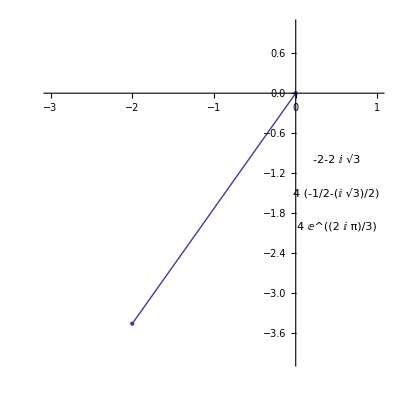

```mathematica
Show[
ListLinePlot[{{0,0},{-2,-2 Sqrt[3]}},AxesOrigin->{0,0}],
ListPlot[{{0,0},{-2,-2 Sqrt[3]}},PlotStyle->PointSize[Medium]],
Graphics[Text[-2-2I Sqrt[3],{0.5,-1}]],
Graphics[Text[4(Cos[2Pi/3]-I Sin[2Pi/3]),{0.5,-1.5}]],
Graphics[Text[4 Exp[I 2Pi/3],{0.5,-2}]],
PlotRange->{{-3,1},{-4,1}},AxesOrigin->{0,0},AspectRatio->1/1]
```

## 2.5.5

```mathematica
ans = Expand[(I+Sqrt[3])^2]
```

2+2 ⅈ √3

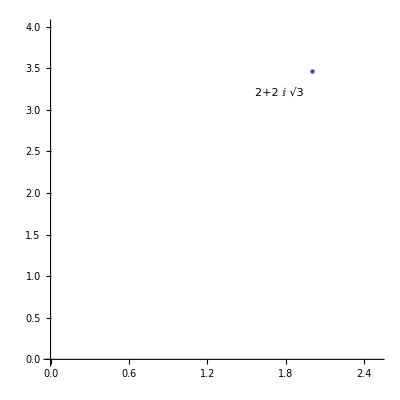

```mathematica
Show[
ListPlot[{{Re[ans],Im[ans]}},
PlotStyle->PointSize[Medium],
PlotRange->{{0,2.5},{0,4}},
AxesOrigin->{0,0},
AspectRatio->1/1],
Graphics[
Text[ans,{1.75,3.2}]
]
]
```

## 2.5.41

```mathematica
Roots[(2x-3y-5)+I(x+2y+1)==0,x]
```

x==(-1/5+(3 ⅈ)/5) ((2-ⅈ)+(5+ⅈ) √3)

```mathematica
Roots[(2x-3y-5)+I(x+2y+1)==0,y]
```

General::ivar: 4\ (-1/2 - √3/2) is not a valid variable.

Roots[-5-12 (-1/2-(√3)/2)+2 x+ⅈ (1+8 (-1/2-(√3)/2)+x)==0,4 (-1/2-(√3)/2)]

## 2.5.59

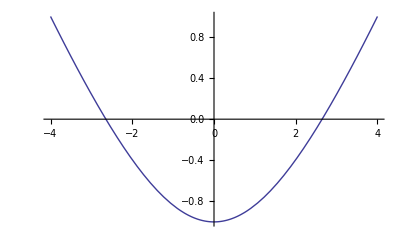

```mathematica
Plot[Abs[z+3I]==4,{z,-4,4}]
```

```mathematica
Reduce[Abs[z+3I]==4,z]
```

z==-4-3 ⅈ||(-4<Re[z]<4&&(Im[z]==-3-√(16-Re[z]^2)||Im[z]==-3+√(16-Re[z]^2)))||z==4-3 ⅈ

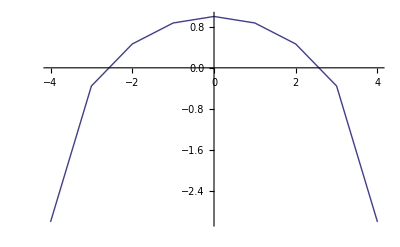

```mathematica
ListPlot[{{-4,-3},{-3,Sqrt[7]-3},{-2,2Sqrt[3]-3},{-1,Sqrt[15]-3},
{0,1},{1,Sqrt[15]-3},{2,2Sqrt[3]-3},{3,Sqrt[7]-3},{4,-3}},
PlotStyle->PointSize[Medium],Joined->True]
```